# Heat stress and bleaching in corals: a bioenergetic model

## Pfab et al, 2024 ferdinand.pfab@gmail.com Code for plotting primary effects of temperature

```mathematica
Get[NotebookDirectory[]<>#]&/@{
(*load model definition*)
"23_10_04_simulation_1.m",
(*load parameter values*)
"23_10_04_parameters_1.m"
};
```

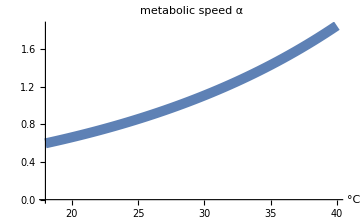

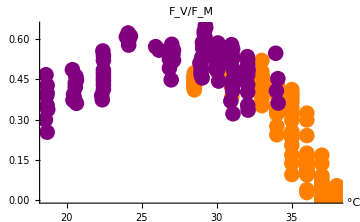
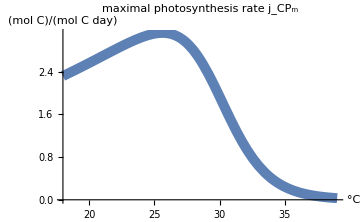

```mathematica
(*Fig. 2*)
FvFmStyle={AxesOrigin->{18,0},AxesLabel->{"°C"},ImageSize->Medium,Ticks->Automatic,PlotRange->Full,LabelStyle->16,PlotRange->{{18,40},Automatic},ImagePadding->{{30,30},{25,20}}};
(Export[NotebookDirectory[]<>"export/Arrhenius.pdf",#];#)&@Plot[α/.rules/.parvalsFvFmArr,{T,18,40},AxesLabel->{"°C",None},Evaluate@FvFmStyle,PlotStyle->Thickness[.02],PlotLabel->"metabolic speed α"] 
(Export[NotebookDirectory[]<>"export/FvFmjCPm.pdf",#];#)&@Style[Row[{

Show[{
ListPlot[{FvFmpointsCunning2023,FvFmpointsBellworthy},PlotMarkers->({Graphics`PlotMarkers[][[1,1]],16}),PlotStyle->{Orange,Purple,Black},Evaluate@FvFmStyle,PlotLabel->Column[{"",Style["F_V/F_M",Italic]},Alignment->Center]]},PlotRange->All],

Plot[jCPm//.rules/.parvalsFvFmArr,{T,18,39},AxesLabel->{"°C",Style["(mol\C)/(mol\C\day)",12]},Evaluate@FvFmStyle,PlotStyle->Thickness[.02],PlotLabel->Column[{"maximal photosynthesis rate","j_CP_m"},Alignment->Center]]},Spacer[15]],LineBreakWithin->False]
```